# Dünne Linsen

## Funktionen

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Abbildungsgleichung(Laplace)

```mathematica
fLaplace[vg_,dvg_,vb_,dvb_]:=Module[{g,b,db,dg,f,fe},
f=1/(1/g+1/b);
fe = GError[f,{g,b},{dg,db}];
{f,fe}/.{g->vg,b->vb,dg->dvg,db->dvb}]
```

### Bessel

```mathematica
fBessel[va_,dva_,ve_,dve_] := Module[{a,e,da,de,f,fe},
f=1/4((a^2-e^2)/a);
fe= GError[f,{a,e},{da,de}];
{f,fe}/.{a->va,e->ve,da->dva,de->dve}]
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

## Laplace

### Berechnung

```mathematica
b = {{2, 1, 1, 1, 1, 1, 1, 1, 1, 1}};
db=0.1;

g = {{2, 7, 6, 5, 4, 3, 3, 2, 2, 1}};
dg=0.2;

f = fLaplace[g[[1]],dg,b[[1]],db];
Grid[f//N,Frame->All]
```

1. | 0.875 | 0.857143 | 0.833333 | 0.8 | 0.75 | 0.75 | 0.666667 | 0.666667 | 0.5
0.075 | 0.0796875 | 0.077551 | 0.075 | 0.072 | 0.06875 | 0.06875 | 0.0666667 | 0.0666667 | 0.075

### Graph

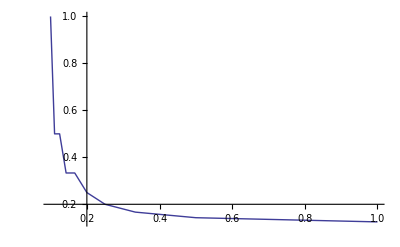

```mathematica
ListLinePlot[Table[{1/b[[1,x]],1/g[[1,x]]},{x,1,Length[b[[1]]]}]]
```

## Bessel Verfahren

### Messung

```mathematica
a2={1,2,3,4,5};
da2=0.1;
e2={1,1.4,1.5,1.7,1.8};
de2=0.2;
f2=Grid[fBessel[a2,da2,e2,de2],Frame->All]
```

0 | 0.255 | 0.5625 | 0.819375 | 1.088
0.15 | 0.10725 | 0.08125 | 0.0720156 | 0.06424

## Zerstreuungslinse

### Methode 1 : ohne/mit Zerstreuung

bo3 ist Abstand von der Sammellinse zum Bild ohne Zerstreuungslinse
bm3 ist der Abstand von der Sammellinse zum Bild mit Zerstreuungslinse
lsz3 ist der Abstand der Linsen
gsz3 ist der Gegenstandsabstand für die Zerstreuungslinse

```mathematica
bo3= {2,2,2,2,2,2,2,2,2,2};
dbo3=0.1;

bm3={3,3,3,3,3,3,3,3,3,3};
dbm3=0.1;

lsz3={1,1,1,1,1,1,1,1,1,1};
dlsz3=0.01;

gz3 =bo3-lsz3;
dgz3 = dbo3+dlsz3;

bz3 = bm3 -lsz3;
dbz3 = dbm3+dlsz3;

f3 = fLaplace[-gz3,dgz3,bz3,dbz3] //N//MatrixForm
```

(-2. | -2. | -2. | -2. | -2. | -2. | -2. | -2. | -2. | -2.
0.55 | 0.55 | 0.55 | 0.55 | 0.55 | 0.55 | 0.55 | 0.55 | 0.55 | 0.55)

### Methode 2 : Bildpunkt der Sammellinse in den Brennpunkt der Zerstreuungslinse legen

lsz4 Abstand Sammellinse zu Zerstreuungslinse
bo4 Abstand Bild ohne Zerstreungslinse

```mathematica
lsz4 = 1;
dlsz4 = 0.1;

bo4 = 3;
dbo4 = 0.1;

f4 = bo4 - lsz4;
df4 = dbo4+lsz4;
{f4,df4}
```

{2,1.1}